```mathematica
o
```

```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2 Mm)/(hbar)^2;
mh2RGM=1/((2.72099 0.529172 137.0373)^2/(938.211+939.505));
Print["ℏ^2/(2 SubscriptBox[m, N]) = ",1/mh2,"=^? ",1/mh2RGM]
```

ℏ^2/(2 SubscriptBox[m, N]) = 20.7355=^? 20.7346

```mathematica
I1[lam_,b1_,b2_] :=(Pi^3)/(3^(1/2)(b1^2+b2^2+2b1 b2+((b1 lam^2)/2)+((b2 lam^2)/2))^(3/2));
I2[lam_,b1_,b2_] := (Pi^3)/((3(b1^2+b2^2+2b1 b2+b1 lam^2+ b2 lam^2+(3lam^4/16)))^(3/2));

I1Joki[lam_,b1_,b2_] :=(2 Pi)^3 /(12 ((b1+b2)^2+2 (b1+b2) lam))^(3/2);
I2Joki[lam_,b1_,b2_] := (2 Pi)^3/(12 ((b1+b2)^2+4 lam (b1+b2)+3 lam^2))^(3/2);
I3[b1_,b2_] :=1/(2 3^(1/2)) b1 b2 (2 Pi)^3/(b1+b2)^4;
```

```mathematica
ham[lam_,b1_,b2_,c0_,d1_,e2_]:=3 c0 I1Joki[0.25 lam^2,b1,b2]+d1 I2Joki[0.25 lam^2,b1,b2]+e2 (1/mh2RGM) I3[b1,b2];

norm[b1_,b2_]:=(2 Pi)^3/(12^(3/2)(b1+b2)^3);
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

λ = 4. fm^-1  :  C_0 = -505.15 MeV    D_1 = 0. MeV

{{-76.003,1.04385},{-76.003,1.06222},{-347.372,-76.003},{ComplexInfinity,ComplexInfinity},{-76.003,0.93051},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{-1396.66,-76.003},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{-76.003,1.05755},{-659.717,-76.003},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{-76.003,1.02418},{ComplexInfinity,ComplexInfinity},{-76.003,-22.9545},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}

{{-76.003,1.1173},{-76.003,1.13099},{-76.003,1.15308},{-76.003,1.15799},{-76.003,1.07543},{-76.003,1.19153},{-76.003,1.20854},{-76.003,0.681006},{-76.003,1.14734},{-76.003,1.16615},{-76.003,1.17402},{-76.003,1.19143},{-76.003,1.19618},{-76.003,1.20892},{-76.003,1.11179},{-76.003,1.15686},{-76.003,1.15418},{-76.003,1.1264},{-76.003,1.09407},{-76.003,1.19419},{-76.003,1.12865},{-76.003,1.17899},{-76.003,1.19998},{-76.003,1.18191},{-76.003,1.16571}}

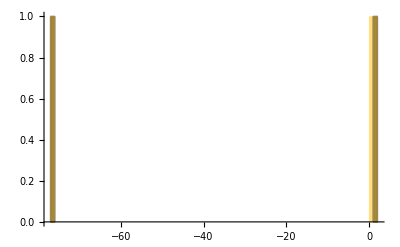

20.7346

```mathematica
λ=4.00;
C0=1.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
D1=0.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];
E2=1.0;
Print["λ = ",λ," fm^-1  :  C_0 = ",C0," MeV    D_1 = ",D1," MeV"]
evlowthreshold=10^-8;
nbrW=25;
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];
gsEresults={};gsEresultsB={};SetSharedVariable[gsEresults,gsEresultsB];

ParallelDo[
dimD=19;
minWi=0.001;
maxWi=0.1+nn 0.43;
sigmi=11.0;
widthsG =Select[RandomVariate[NormalDistribution[maxWi,sigmi],dimD],#>0&];
widthsL = N@logspace[dimD-1,0.02,2+maxWi];
widths=Join[widthsG,widthsL];
dimD=Length[widths];

hamm=Table[ham[λ,widths[[i]],widths[[j]],C0,D1,E2],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
AppendTo[gsEresultsB,evBare[[1;;2]]];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(*Print[Length[μ]];*)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
esh=Eigensystem[traham];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];
(*Print["E_0^(bare) = ",Sort[evBare][[1]]];*)
If[Select[ϵ,#<1.0&]≠{},
AppendTo[gsEresults,ϵ[[1;;2]]]
(*Print["Dim - Dim_reduced = ",dimD," - ",Length[μ],"     0H0 = ",gsh.traham.gsh," =^! ",ϵ[[1]],"   E_0^(bare) = ",Sort[evBare][[;;4]]]*)
];
,{nn,Range[1,nbrW]}]
Sort[gsEresultsB,Re[#1]<Re[#2]&]
Sort[gsEresults,#1<#2&]
Histogram[gsEresults,{1}]
```

```mathematica
dimD=122;
maxWi=2.43;
sigmi=25.0;
widths =Select[RandomVariate[NormalDistribution[maxWi,sigmi],dimD],#>0&];
dimD=Length[widths];

hamm=Table[ham[λ,widths[[i]],widths[[j]],C0,D1,E2],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

normm//MatrixForm;

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

NormN//MatrixForm;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
evBareN=Sort[Eigenvalues[{HamN,NormN}],Re[#1]<Re[#2]&];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];

trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
trano=(Transpose[trafma].NormN).trafma;

esh=Eigensystem[{traham,trano}];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];

{evBare[[1]],evBareN[[1]],ϵ[[1]]}
```

{-16779.5,ComplexInfinity,-150.654}

```mathematica
bnd=40;
ai=2;aj=1;lamm=1.4;
(* Subscript[δ, 12] Subscript[δ, 13] and Subscript[δ, 23] Subscript[δ, 13] and Subscript[δ, 12] Subscript[δ, 23] yield the same result *)
kernel3[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la ((x1-x2)^2+(x1-(-x1-x2))^2)];

nInt3=NIntegrate[kernel3[xa,xb,ai,aj,lamm],{xa,-bnd,bnd},{xb,-bnd,bnd}];
aInt3=(2 π)^3/((12 ((ai+aj)^2+3 lamm^2+4 lamm (ai+aj)))^(3/2));
Print["numerical:  ",nInt^3]
Print["analytical: ",N[aInt]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

numerical:  nInt^3

analytical: aInt

```mathematica
kernel12[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la (x1-x2)^2];
kernel13[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la (2 x1+x2)^2];
kernel23[x1_,x2_,b1_,b2_,la_]:=Exp[-2 (b1+b2) (x1^2+x2^2+x1 x2)-la (x1+2 x2)^2];
nInt12=NIntegrate[kernel23[xa,xb,ai,aj,lamm],{xa,-bnd,bnd},{xb,-bnd,bnd}];
aInt12=(2 π)^3/((12 ((ai+aj)^2+2 lamm (ai+aj)))^(3/2));
Print["numerical:  ",nInt12^3]
Print["analytical: ",N[aInt12]]
```

numerical:  0.0822129

analytical: 0.0822136

```mathematica
Simplify[-2/3 (D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],x1] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],x1]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],y1] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],y1]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],z1] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],z1]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],x2] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],x2]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],y2] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],y2]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],z2] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],z2])
+1/3 (D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],x1] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],x2]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],y1] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],y2]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],z1] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],z2]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],x2] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],x1]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],y2] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],y1]+D[Exp[-(a1 x1^2+a1 y1^2+a1 z1^2+b1 x2^2+b1 y2^2+b1 z2^2+c1 (x1+x2)^2+c1 (y1+y2)^2+c1 (z1+z2)^2)],z2] D[Exp[-(a2 x1^2+a2 y1^2+a2 z1^2+b2 x2^2+b2 y2^2+b2 z2^2+c2 (x1+x2)^2+c2 (y1+y2)^2+c2 (z1+z2)^2)],z1])]
```

-4/3 ⅇ^(-a1 x1^2-a2 x1^2-b1 x2^2-b2 x2^2-c1 (x1+x2)^2-c2 (x1+x2)^2-a1 y1^2-a2 y1^2-b1 y2^2-b2 y2^2-c1 (y1+y2)^2-c2 (y1+y2)^2-a1 z1^2-a2 z1^2-b1 z2^2-b2 z2^2-c1 (z1+z2)^2-c2 (z1+z2)^2) (2 c1 c2 x1^2+b2 c1 x1 x2+b1 c2 x1 x2+4 c1 c2 x1 x2+2 b1 b2 x2^2+b2 c1 x2^2+b1 c2 x2^2+2 c1 c2 x2^2+2 c1 c2 y1^2+b2 c1 y1 y2+b1 c2 y1 y2+4 c1 c2 y1 y2+2 b1 b2 y2^2+b2 c1 y2^2+b1 c2 y2^2+2 c1 c2 y2^2+2 c1 c2 z1^2+b2 c1 z1 z2+b1 c2 z1 z2+4 c1 c2 z1 z2+2 b1 b2 z2^2+b2 c1 z2^2+b1 c2 z2^2+2 c1 c2 z2^2-a2 b1 (x1 x2+y1 y2+z1 z2)+a2 c1 (x1^2+x1 x2+y1^2+y1 y2+z1 (z1+z2))+a1 (2 a2 (x1^2+y1^2+z1^2)-b2 (x1 x2+y1 y2+z1 z2)+c2 (x1^2+x1 x2+y1^2+y1 y2+z1 (z1+z2))))

analytical - numerical comparison for a norm matrix element (2-body):

```mathematica
bnd=50;
ai=0.0231;aj=0.33;bi=0.31;bj=0.33;ci=0.021;cj=1.3;
kernelT[x1_,x2_,y1_,y2_,z1_,z2_,a1_,a2_,b1_,b2_,c1_,c2_]:=-4/3 ⅇ^(-a1 x1^2-a2 x1^2-b1 x2^2-b2 x2^2-c1 (x1+x2)^2-c2 (x1+x2)^2-a1 y1^2-a2 y1^2-b1 y2^2-b2 y2^2-c1 (y1+y2)^2-c2 (y1+y2)^2-a1 z1^2-a2 z1^2-b1 z2^2-b2 z2^2-c1 (z1+z2)^2-c2 (z1+z2)^2) (2 c1 c2 x1^2+b2 c1 x1 x2+b1 c2 x1 x2+4 c1 c2 x1 x2+2 b1 b2 x2^2+b2 c1 x2^2+b1 c2 x2^2+2 c1 c2 x2^2+2 c1 c2 y1^2+b2 c1 y1 y2+b1 c2 y1 y2+4 c1 c2 y1 y2+2 b1 b2 y2^2+b2 c1 y2^2+b1 c2 y2^2+2 c1 c2 y2^2+2 c1 c2 z1^2+b2 c1 z1 z2+b1 c2 z1 z2+4 c1 c2 z1 z2+2 b1 b2 z2^2+b2 c1 z2^2+b1 c2 z2^2+2 c1 c2 z2^2-a2 b1 (x1 x2+y1 y2+z1 z2)+a2 c1 (x1^2+x1 x2+y1^2+y1 y2+z1 (z1+z2))+a1 (2 a2 (x1^2+y1^2+z1^2)-b2 (x1 x2+y1 y2+z1 z2)+c2 (x1^2+x1 x2+y1^2+y1 y2+z1 (z1+z2))));
nIntT=NIntegrate[kernelT[xa,xb,ya,yb,za,zb,ai,aj,bi,bj,ci,cj],{xa,-bnd,bnd},{xb,-bnd,bnd},{ya,-bnd,bnd},{yb,-bnd,bnd},{za,-bnd,bnd},{zb,-bnd,bnd}];
aIntT=(8/3) ((2 Pi)^3/(32 ((ai+aj+ci+cj)(bi+bj+ci+cj)-(ci+cj)^2)^2.5))((aj ci+cj ai+2ci cj+2ai aj)(bi+ci+bj+cj)+(bi cj+bj ci+2ci cj+2bi bj)(ai+aj+ci+cj)-(cj(ai+bi)+ci(aj+bj)-bj ai-aj bi+4ci cj)(ci+cj));
Print["numerical:  ",nIntT]
Print["analytical: ",N[aIntT]]
nIntT/aIntT
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -15.6813 and 0.284406 for the integral and error estimates.

numerical:  -15.6813

analytical: 5.21721

-3.00569

analytical - numerical comparison for a norm matrix element (3-body):

```mathematica
SpaceDim=3;
Ax=4 "α_ij" {{1,1/2},{1/2,1}};
Amat=KroneckerProduct[IdentityMatrix[SpaceDim],Ax];iAmat=Inverse[Amat];
Print["A̲ = ",Amat//MatrixForm,"       det(A̲) = ",Det[Amat],"       (A̲)^-1 = ",iAmat//MatrixForm]
```

A̲ = (4 α_ij | 2 α_ij | 0 | 0 | 0 | 0
2 α_ij | 4 α_ij | 0 | 0 | 0 | 0
0 | 0 | 4 α_ij | 2 α_ij | 0 | 0
0 | 0 | 2 α_ij | 4 α_ij | 0 | 0
0 | 0 | 0 | 0 | 4 α_ij | 2 α_ij
0 | 0 | 0 | 0 | 2 α_ij | 4 α_ij)       det(A̲) = 1728 α_ij^6       (A̲)^-1 = (1/(3 α_ij) | -1/(6 α_ij) | 0 | 0 | 0 | 0
-1/(6 α_ij) | 1/(3 α_ij) | 0 | 0 | 0 | 0
0 | 0 | 1/(3 α_ij) | -1/(6 α_ij) | 0 | 0
0 | 0 | -1/(6 α_ij) | 1/(3 α_ij) | 0 | 0
0 | 0 | 0 | 0 | 1/(3 α_ij) | -1/(6 α_ij)
0 | 0 | 0 | 0 | -1/(6 α_ij) | 1/(3 α_ij))

```mathematica
FactorInteger[1728]
2^6 3^3
```

{{2,6},{3,3}}

1728

```mathematica
Format[α[m_,n_,d_]]:=Subscript[α,m,n]^(d)
SpaceDim=3;
Ax=2 {{α[1,1,"n"]+α[1,3,"n"]+α[1,1,"m"]+α[1,3,"m"],α[1,3,"n"]+α[1,3,"m"]},{α[1,3,"n"]+α[1,3,"m"],α[1,2,"n"]+α[1,3,"n"]+α[1,2,"m"]+α[1,3,"m"]}};
Amat=KroneckerProduct[IdentityMatrix[SpaceDim],Ax];iAmat=Inverse[Amat];
Print["A̲ = ",Amat//MatrixForm,"       det(A̲) = ",Simplify[Det[Amat]],"       (A̲)^-1 = ",iAmat//MatrixForm]
```

A̲ = (2 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) | 2 (α_(1,3)^m+α_(1,3)^n) | 0 | 0 | 0 | 0
2 (α_(1,3)^m+α_(1,3)^n) | 2 (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) | 0 | 0 | 0 | 0
0 | 0 | 2 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) | 2 (α_(1,3)^m+α_(1,3)^n) | 0 | 0
0 | 0 | 2 (α_(1,3)^m+α_(1,3)^n) | 2 (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) | 0 | 0
0 | 0 | 0 | 0 | 2 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) | 2 (α_(1,3)^m+α_(1,3)^n)
0 | 0 | 0 | 0 | 2 (α_(1,3)^m+α_(1,3)^n) | 2 (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))       det(A̲) = 64 ((α_(1,3)^m+α_(1,3)^n)^2-(α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))^2 (-(α_(1,3)^m+α_(1,3)^n)^2+(α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))       (A̲)^-1 = ((2 (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | -(2 (α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | 0 | 0 | 0 | 0
-(2 (α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | (2 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | 0 | 0 | 0 | 0
0 | 0 | (2 (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | -(2 (α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | 0 | 0
0 | 0 | -(2 (α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | (2 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | 0 | 0
0 | 0 | 0 | 0 | (2 (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | -(2 (α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))
0 | 0 | 0 | 0 | -(2 (α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))) | (2 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))))/(-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2 (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n))+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n) (-4 (α_(1,3)^m+α_(1,3)^n)^2+4 (α_(1,1)^m+α_(1,1)^n+α_(1,3)^m+α_(1,3)^n) (α_(1,2)^m+α_(1,2)^n+α_(1,3)^m+α_(1,3)^n)))))

```mathematica
bnd=10;
ai=0.21;aj=0.15;bi=0.51;bj=0.15;ci=0.51;cj=0.15;
kernel4[x1_,x2_,y1_,y2_,z1_,z2_,a1_,a2_,b1_,b2_,c1_,c2_]:=ⅇ^(-((a1+a2+c1+c2) x1^2+2 (c1+c2) x1 x2+(b1+b2+c1+c2) x2^2+(a1+a2+c1+c2) y1^2+2 (c1+c2) y1 y2+(b1+b2+c1+c2) y2^2+(a1+a2+c1+c2) z1^2+2 (c1+c2) z1 z2+(b1+b2+c1+c2) z2^2));
nIntT=NIntegrate[kernel4[xa,xb,ya,yb,za,zb,ai,aj,bi,bj,ci,cj],{xa,-bnd,bnd},{xb,-bnd,bnd},{ya,-bnd,bnd},{yb,-bnd,bnd},{za,-bnd,bnd},{zb,-bnd,bnd}];
aIntT=(2 π)^3/(8 ((ai+aj+ci+cj) (bi+bj+ci+cj)-(ci+cj)^2)^1.5);
Print["numerical:  ",nIntT]
Print["analytical: ",N[aIntT]]
nIntT/aIntT
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 35.6517 and 0.152681 for the integral and error estimates.

numerical:  35.6517

analytical: 35.671

0.99946

```mathematica
AMA={{4 (a1+a2)+10 λ,2 (a1+a2)+8 λ},{2 (a1+a2)+8 λ,4 (a1+a2)+10 λ}};
iAMA=Simplify[Inverse[AMA]];
AMA//MatrixForm
iAMA//MatrixForm
Simplify[Det[AMA]]
```

(40.+4 (a1+a2) | 32.+2 (a1+a2)
32.+2 (a1+a2) | 40.+4 (a1+a2))

((0.333333 (10.+a1+a2))/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2) | (-2.66667-0.166667 a1-0.166667 a2)/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2)
(-2.66667-0.166667 a1-0.166667 a2)/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2) | (0.333333 (10.+a1+a2))/(48.+16. a1+a1^2+16. a2+2. a1 a2+a2^2))

12. (48.+a1^2+16. a2+a2^2+a1 (16.+2. a2))

```mathematica
AMA={{4 (a1+a2),2 (a1+a2)},{2 (a1+a2),4 (a1+a2)}};
iAMA=Simplify[Inverse[AMA]];
AMA//MatrixForm
iAMA//MatrixForm
Simplify[((2 π)/(√Det[AMA]))^3 (-2/3 (4 a1 a2 (3 iAMA[[1,1]]+3 iAMA[[2,2]]))+1/3(4 a1 a2 (3 iAMA[[1,2]]+3 iAMA[[2,1]])))]
```

(4 (a1+a2) | 2 (a1+a2)
2 (a1+a2) | 4 (a1+a2))

(1/(3 a1+3 a2) | -1/(6 (a1+a2))
-1/(6 (a1+a2)) | 1/(3 a1+3 a2))

-(20 a1 a2 π^3)/(9 √3 (a1+a2)^3 √((a1+a2)^2))

general Gaussian expansion (see  so-called ‘’stochastic-variational method’’ of Y. Suzuki & K. Varga):
i:=e^(-α_i·(r̄)_1^2-β_i·(r̄)_2^2-γ_i·(r̄)_3^2)

```mathematica
AMA=2 {{("α"+"γ"),"γ"},{"γ",("β"+"γ")}};
AMAp=2 {{("α'"+"γ'"),"γ'"},{"γ'",("β'"+"γ'")}};
AM=AMA+AMAp;
iAM=Simplify[Inverse[AM]];
AL2=2 {{"λ",-"λ"},{-"λ","λ"}};
AL3={{4 "λ",2 "λ"},{2 "λ",10 "λ"}};
```

```mathematica
Tmat[a_,b_,c_,ap_,bp_,cp_,hbm_]:=
(-hbm) (-2) ((2 π)/(√Det[AM]))^3  ((AMA[[1,1]] AMAp[[1,1]]-1/2 (AMA[[1,1]] AMAp[[1,2]]+AMAp[[1,1]] AMA[[1,2]])+AMA[[1,2]] AMAp[[1,2]]) iAM[[1,1]]+(AMA[[2,2]] AMAp[[2,2]]-1/2 (AMA[[2,2]] AMAp[[1,2]]+AMAp[[2,2]] AMA[[1,2]])+AMA[[1,2]] AMAp[[1,2]]) iAM[[2,2]]+(AMAp[[1,2]] (AMA[[1,1]]+AMA[[2,2]])+AMA[[1,2]] (AMAp[[1,1]]+AMAp[[2,2]])-1/2 (AMA[[1,1]] AMAp[[2,2]]+AMAp[[1,1]] AMA[[2,2]])-AMA[[1,2]] AMAp[[1,2]]) iAM[[1,2]])/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp}
V2mat[a_,b_,c_,ap_,bp_,cp_,lam_,c0_]:=(c0 ((2 π)/(√Det[AM+AL2]))^3)/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp,"λ"->lam}
V3mat[a_,b_,c_,ap_,bp_,cp_,lam_,d1_]:=(d1 ((2 π)/(√Det[AM+AL3]))^3)/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp,"λ"->lam}
Nmat[a_,b_,c_,ap_,bp_,cp_]:=(((2 π)/(√Det[AM]))^3)/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp}
```

consistency with ‘’hyper-radial expansion’’:

```mathematica
Print["-ℏ/(2 SubscriptBox[m, nucl])∫d(OverBar[r̲]_1,OverBar[r̲]_2)e^(-FractionBox[1, 2] SuperscriptBox[r, T]·A·r)(-2/3((∂^↼)_x_1·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_2)+1/3((∂^↼)_x_1·OverVector[∂]_x_2+…+(∂^↼)_z_1·OverVector[∂]_z_2+(∂^↼)_x_2·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_1))e^(-FractionBox[1, 2] SuperscriptBox[r, T]·SuperscriptBox[A, ']·r) = ",Simplify[Tmat[α,α,α,α',α',α',"ℏ/(2 SubscriptBox[m, N])"]]]
Simplify[V2mat[α,α,α,α',α',α',"λ","C_0"]]
Simplify[V3mat[α,α,α,α',α',α',"λ","D_1"]]
```

-ℏ/(2 SubscriptBox[m, nucl])∫d(OverBar[r̲]_1,OverBar[r̲]_2)e^(-FractionBox[1, 2] SuperscriptBox[r, T]·A·r)(-2/3((∂^↼)_x_1·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_2)+1/3((∂^↼)_x_1·OverVector[∂]_x_2+…+(∂^↼)_z_1·OverVector[∂]_z_2+(∂^↼)_x_2·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_1))e^(-FractionBox[1, 2] SuperscriptBox[r, T]·SuperscriptBox[A, ']·r) = (4 ℏ/(2 SubscriptBox[m, N]) π^3 α α')/(√3 (α+α')^3 √((α+α')^2))

(C_0 π^3)/(3 √3 ((α+α') (2 λ+α+α'))^(3/2))

(D_1 π^3)/(3 √3 (3 λ^2+4 λ α+α^2+2 (2 λ+α) α'+(α')^2)^(3/2))

```mathematica
ham[lam_,A_,Ap_,c0_,d1_]:=3 V2mat[A[[1]],A[[2]],A[[3]],Ap[[1]],Ap[[2]],Ap[[3]],0.25 lam^2,c0];

norm[A_,Ap_]:=Nmat[A[[1]],A[[2]],A[[3]],Ap[[1]],Ap[[2]],Ap[[3]]];
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

λ = 4. fm^-1  :  C_0 = -505.15 MeV    D_1 = 0. MeV

{-1351.88,-1331.2,-1324.61,-1323.03,-1313.35,-1312.33,-1309.51,-1307.07,-1305.24,-1303.52,-1299.36,-1296.17,-1284.76,-1268.97,-1268.73,-1254.44,-1246.99,-1244.7,-1243.26,-1240.58,-1219.36,-1207.06,-1202.27,-1171.92,-1161.05}

{-1351.88,-1331.2,-1324.61,-1323.03,-1313.35,-1312.33,-1309.51,-1307.07,-1305.24,-1303.52,-1299.36,-1296.17,-1284.76,-1268.97,-1268.73,-1254.44,-1246.99,-1244.7,-1243.26,-1240.58,-1219.36,-1207.06,-1202.27,-1171.92,-1161.05}

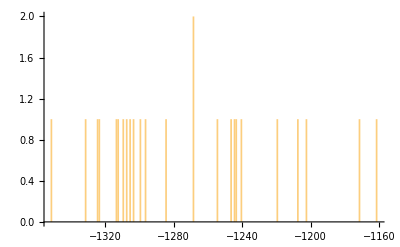

```mathematica
λ=4.00;
C0=1.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
D1=0.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];

Print["λ = ",λ," fm^-1  :  C_0 = ",C0," MeV    D_1 = ",D1," MeV"]
evlowthreshold=10^-8;
nbrW=25;
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];
gsEresults={};gsEresultsB={};SetSharedVariable[gsEresults,gsEresultsB];

ParallelDo[
dimD=14;
cent=0.1+nn 0.43;
sigmi=11.0;

widthsG={};
ll=0;
While[ll<3 dimD,
widthsG=Join[widthsG ,Select[RandomVariate[NormalDistribution[cent,sigmi],dimD],#>0&]];
ll=Length[widthsG]
];
widths=Partition[widthsG,dimD][[;;3]];

hamm=Table[ham[λ,widths[[All,i]],widths[[All,j]],C0,D1],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[All,i]],widths[[All,j]]],{i,dimD},{j,dimD}];

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
AppendTo[gsEresultsB,evBare[[1]]];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(*Print[Length[μ]];*)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
esh=Eigensystem[traham];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];
(*Print["E_0^(bare) = ",Sort[evBare][[1]]];*)
If[Select[ϵ,#<1.0&]≠{},
AppendTo[gsEresults,ϵ[[1]]]
(*Print["Dim - Dim_reduced = ",dimD," - ",Length[μ],"     0H0 = ",gsh.traham.gsh," =^! ",ϵ[[1]],"   E_0^(bare) = ",Sort[evBare][[;;4]]]*)
];
,{nn,Range[1,nbrW]}]
Sort[gsEresultsB,Re[#1]<Re[#2]&]
Sort[gsEresults,#1<#2&]
Histogram[gsEresults,{1}]
```

```mathematica
bnd=20;
ai=0.231;aj=1.33;
kernelT[x1_,y1_,z1_,b1_,b2_]:=2 ⅇ^(-4 (b1+b2) (x1^2+y1^2+z1^2)) (x1^2+y1^2+z1^2);
nIntT=NIntegrate[kernelT[xa,ya,za,ai,aj],{xa,-bnd,bnd},{ya,-bnd,bnd},{za,-bnd,bnd}];
aIntT=(2 3 (2 π)^(3/2))/(8 (ai+aj))^(5/2);
Print["numerical:  ",nIntT]
Print["analytical: ",N[aIntT]]
nIntT/aIntT
```

numerical:  0.17147

analytical: 0.17147

1.

```mathematica
bnd=20;
ai=0.231;aj=1.33;
kernelT[x1_,y1_,z1_,b1_,b2_]:=4 ⅇ^(-4 (b1+b2) (x1^2+y1^2+z1^2)) (x1^4+y1^4+z1^4+2 x1^2 y1^2+2 x1^2 z1^2+2 y1^2 z1^2)^1;
nIntT=NIntegrate[kernelT[xa,ya,za,ai,aj],{xa,-bnd,bnd},{ya,-bnd,bnd},{za,-bnd,bnd}];
aIntT=(4 5 3 (2 π)^(3/2))/(8 (ai+aj))^(7/2);
Print["numerical:  ",nIntT]
Print["analytical: ",N[aIntT]]
nIntT/aIntT
```

numerical:  0.137308

analytical: 0.137308

1.

```mathematica
Eigensystem
```